#### 3. domača naloga

### Naloga 1

Definirajmo konstante in ustrezne vektorje.

```mathematica
v0={10,3};
GG=9.81;
H=10;
a = {0, -GG};
x0 ={0, H};
```

Formule iz fizike, nam povedo naslednje:
v(t) = v_o + a t
x(t) = x_o + v_ot + at^2/2

Z upoštevanjem teh formul lahko zapišemo naslednji izraz.

```mathematica
v[t_] :={v0[[1]], v0[[2]] - GG*t}
```

Lahko pa zgornji enačbi zapišemo tudi v vektorski obliki, saj sta veljavni za vsako komponento posebej.

```mathematica
{v0[[1]], v0[[2]] - GG*t}
v0 + a*t
```

{10,3-9.81 t}

{10,3-9.81 t}

Zapišimo sedaj obe funkciji kar preko vektorske oblike. Pozor: namesto simbola "mali x" smo uporabili simbol "veliki X". To pa zato, ker si ponavadi simbolov x, y, ... ne želimo "zasesti", saj imamo potem tipično težave pri reševanju enačb.

```mathematica
v[t_] := v0 + a*t
X[t_] := x0 + v0*t + a*t^2/2
```

Točko določa funkcija X[t]. S pomočjo te sestavimo ustrezen grafični objekt.

```mathematica
SlikaTocke[t_] := {PointSize[0.03],Point[X[t]]};
```

Oglejmo si rezultat. Pri vrednosti t = 1

```mathematica
Graphics[SlikaTocke[1]]
```

-Graphics-

Sama slika brez koordinatnih osi nam ne pove nič. Dodajmo koordinatne osi ter nastavimo območje izrisa.

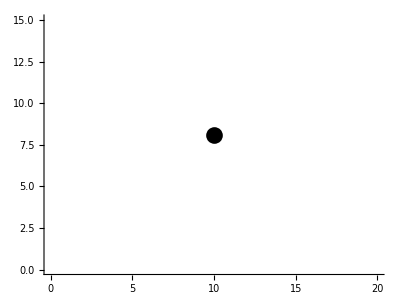

```mathematica
Graphics[SlikaTocke[1], Axes->True, PlotRange-> {{0,20}, {0, 15}}]
```

Poigrajmo se malce s funkcijo Manipulate, da si ogledamo, kako se giblje točka.

```mathematica
Manipulate[Graphics[SlikaTocke[t], Axes->True, PlotRange-> {{0,20}, {0, 15}}], {t, 0, 3}]
```

Kako se že nariše puščico?

```mathematica
Manipulate[Graphics[{SlikaTocke[t], Arrow[{{1,1}, {2,2}}]}, Axes->True, PlotRange-> {{0,20}, {0, 15}}], {t, 0, 3}]
```

### Naloga 2

Sestavimo si "testno" ravnino

```mathematica
r111 = Ravnina[{-1,-1,-1},{1,1,1}]
```

-Graphics3D-

3D Grafični objekt z uporabo Hyperplane.

```mathematica
Slika[Ravnina[n_, v_]] :=Hyperplane[n, v]
```

Definirana funkcija Format Mathematici sporoča, kako naj se nek objekt prikaže. Primer

```mathematica
Format[t_Trikotnik] := "En čuden trikotnik ..."
```

```mathematica
Trikotnik[1,2,3]
```

En čuden trikotnik ...

Prikaz je lahko kateri koli izraz v Mathematici. Če pa je ta izraz slika, se objekt pač prikaže kot slika.

```mathematica
Format[r_Ravnina] := Graphics3D[Slika[r]]
```

```mathematica
r111
```

-Graphics3D-

Definirajmo "koordinatno" ravnino za os x.

```mathematica
rx=Ravnina[{1, 0, 0}, {0, 0, 0}];
```

Slika normale.

```mathematica
SlikaNormale[Ravnina[n_, v_]] :=Arrow[{v, v + n}]
```

Primeri

```mathematica
Graphics3D[{Slika[r111],SlikaNormale[r111]}]
```

-Graphics3D-

Kako izrišemo več ravnin?

```mathematica
ravnine = {r111, rx};
obeSliki[r_Ravnina] := {Slika[r],SlikaNormale[r]}
Graphics3D[Map[obeSliki, ravnine]]
```

-Graphics3D-

Poenostavitev zapisa, da se izognemo definiciji ločene funkcije. Definiramo “anonimno” funkcijo na mestu uporabe (# - parameter funkcije, & - konec definicije).

```mathematica
Graphics3D[Map[{Slika[#],SlikaNormale[#]}&, ravnine]]
```

-Graphics3D-

Še en primer z uporabo t.i. veriženja preko operatorja //, kot gurmanski dodatek za sladokusce :) . Zapis z veriženjem (rezultat prejšnjega izraza gre v prosti parameter naslednjega izraza) je včasih bolj pregleden zapis, ker mogoče raje zaporedje ukazov beremo iz leve proti desni. Lepo ga preberemo:
- najprej imamo ravnine
- potem “čez njih Map-nemo” funkcijo obeSliki
- potem rezultat predamo funkciji, ki vse skupaj objame z Graphics.

```mathematica
ravnine //
Map[obeSliki, #]& //
   Graphics3D[#]&
```

-Graphics3D-

Nariši vse štiri ravnine rx, ry, rz, r111 na isti sliki skupaj z normalami.

```mathematica
rx = Ravnina[{1, 0, 0}, {0, 0, 0}];
ry = Ravnina[{0, 1, 0}, {0, 0, 0}];
rz = Ravnina[{0, 0, 1}, {0, 0, 0}];
```

```mathematica
ravnine = {r111, rx, ry, rz};
vseSlike[r_Ravnina] := {Slika[r],SlikaNormale[r]};
Graphics3D[Map[vseSlike, ravnine]]
```

-Graphics3D-

Sestavi funkcijo Enacba[Ravnina[n_, v_]], ki vrne enačbo ravnine.

```mathematica
Enacba[Ravnina[n_, v_]] := Module[{a, b, c, d},
	a = n[[1]];
	b = n[[2]];
	c = n[[3]]; 
	d = a*v[[1]] + b*v[[2]] + c*v[[3]];
	a*x + b*y + c*z == d]
```

```mathematica
Enacba[r111]
```

-x-y-z==-3

Sestavi funkcijo ResiSistem[sistem_List],ki za dan sistem treh enačb v spremenljivkah x,y in z vrne točko rešitve.Predpostavi,da je sistem takšen,da vrne samo eno rešitev.

```mathematica
SezEnacb = List[Enacba[r111], Enacba[rx], Enacba[ry]];
ResiSistem[sistem_List] := Solve[{sistem[[1]], sistem[[2]], sistem[[3]]}, 
	{x, y, z}]
```

```mathematica
ResiSistem[SezEnacb]
```

{{x→0,y→0,z→3}}

#### Naloga 3

```mathematica
Graphics3D[Pyramid[{{0,0,0},{6,0,0},{6,4,0},{4,2,0},{4,1,2}}]]
```

-Graphics3D-

S funkcijo Parellelepiped lahko ob pravilni izbiri smeri narišemo tudi kvader.

```mathematica
Graphics3D[Parallelepiped[{0,0,0},{{0,0,1},{2,0,0},{0,3,0}}]]
```

-Graphics3D-

In še en čisto pravi paralelepiped. :)

```mathematica
izhodisce ={0,0,0};
s1={1,2,3};
s2={4,5,6};
s3={7,8,2};
Graphics3D[Parallelepiped[izhodisce,{s1,s2,s3}]]
```

-Graphics3D-

```mathematica
SetOptions[EvaluationNotebook[],Background-> Lighter[Lighter[Lighter[Magenta]]] ]
```